# 棋盘格错觉

### https://tywkiwdbi.blogspot.com/2014/01/all-lines-in-this-checkerboard-pattern.html

### 效果图

## 实现过程

## 绘制棋盘格背景

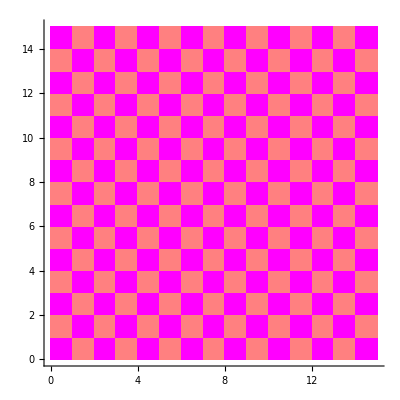

```mathematica
Graphics[{Table[{If[EvenQ[i+j],Magenta,Pink],Rectangle[{i,j}-1]},{i,1,15},{j,1,15}]},Axes->True]
```

### 另一种方式

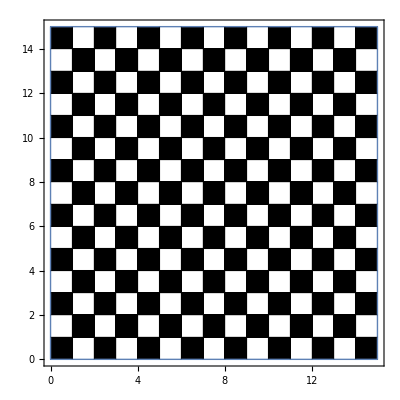

```mathematica
ParametricPlot[{i,j},{i,0,15},{j,0,15},Mesh->14,MeshShading->{{Black,None},{None,Black}}]
```

## 绘制棋盘格上的圆点

通过观察可以发现这样的规律

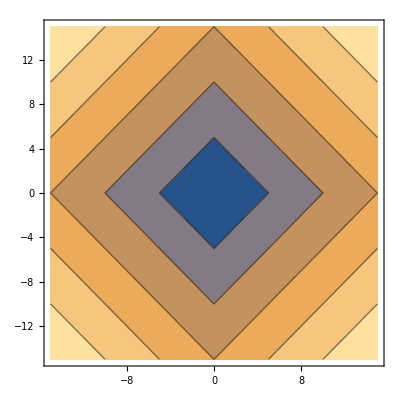

```mathematica
ContourPlot[Abs[x]+Abs[y],{x,-15,15},{y,-15,15}]
```

使用Graphics绘制出来

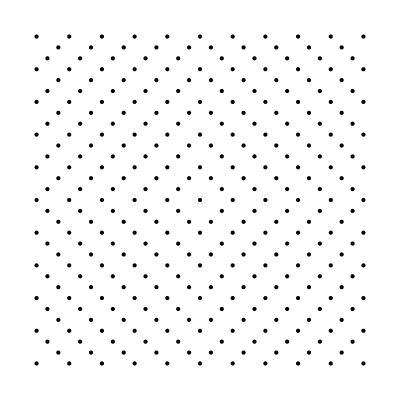

```mathematica
Graphics[Point@Union@Flatten[Table[k=Abs[x]+Abs[y];If[Mod[k,3]==0,{x,y},Nothing],{x,-15,15},{y,-15,15}],1]]
```

继续增加额外的条件约束要生成圆点的位置，并添加颜色

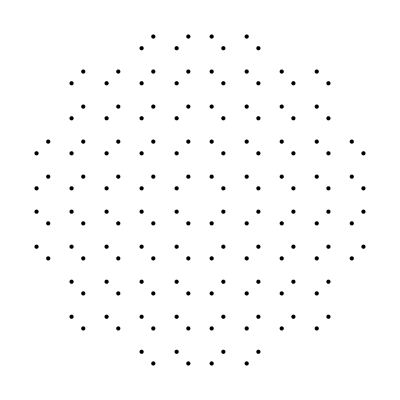

```mathematica
Graphics[{PointSize[Large],Union@Flatten[Table[k=Abs[x]+Abs[y];If[Mod[k,3]==0&&Mod[x,3]!=0&&Norm[{x,y}]<15,Point[{x,y},VertexColors->If[Mod[k,6]==0,Pink,Magenta]],Nothing],{x,-15,15},{y,-15,15}],1]},GridLines->Automatic]
```

### 将棋盘格和圆点组合在一起，稍微修改一下参数

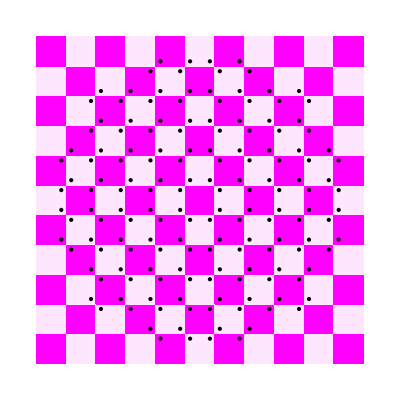

```mathematica
Graphics[{Table[{If[EvenQ[i+j],Magenta,LightMagenta],Rectangle[{i,j}-1.5,{i,j}+1.5]},{i,-15,15,3},{j,-15,15,3}],PointSize[Large],Union@Flatten[Table[k=Abs[x]+Abs[y];If[Mod[k,3]==0&&Mod[x,3]!=0&&Norm[{x,y}]<15,Point[{x,y},VertexColors->If[Mod[k,6]==0,LightMagenta,Magenta]],Nothing],{x,-15,15},{y,-15,15}],1]},GridLines->Automatic]
```

## 优化代码

上面的代码虽然可以正常实现我们想要的效果，
但是逻辑有些冗余，
让我们尝试简化，使用更少的代码来完成

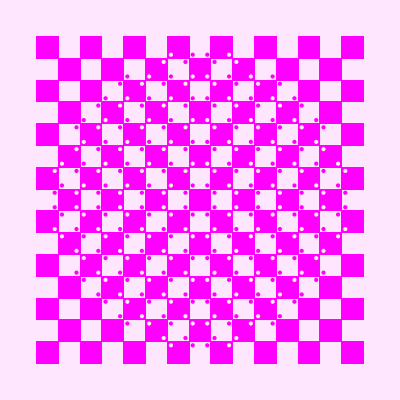

```mathematica
r=21;m=Mod;Graphics[{PointSize[Large],Table[p={x,y};k=Abs@x+Abs@y;{Magenta,If[m[x+1,3]+m[x+y+2,6]==0,Rectangle[p,p+3]],If[m[k,6]==0,LightPink],If[m[k,3]==0&&m[x,3]!=0&&Norm@p<r-.5,Point[p+.5]]},{x,-r-1,r},{y,-r-2,r}]},Background->LightMagenta]
```

### 过程很伤脑筋，但总算完成了。 好了，不求完美。